```mathematica
{a, b}×{x,y}
```

{a,b}×{x,y}

```mathematica
{a,b,c}×{x,y,z}
```

{-c y+b z,c x-a z,-b x+a y}

```mathematica
{a,b}.{x,y}
```

a x+b y

```mathematica
{a,b,c}.{x,y,z}
```

a x+b y+c z

```mathematica
Det[({{Subscript[a, 1,1], Subscript[a, 1,2]}, {Subscript[a, 2,1], Subscript[a, 2,2]}})]
```

-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)

```mathematica
ArcCos[(√2)/2]/(π/180)
```

45

```mathematica
A={{0.8,0.8},{0.4,1.6}};
v⃗={-3,2};
ListPlot[{A .v⃗,(A^2) .v⃗,(A^3) .v⃗,(A^4) .v⃗,(A^5) .v⃗,(A^6) .v⃗,(A^7) .v⃗}]
```

```mathematica
A={{2,0},{1,3}};v⃗={2,1};w⃗={0,3};
{A.A,A^2,A×A,A*A}
{A.v⃗,A.w⃗,A.A}
```

{{{4,0},{5,9}},{{4,0},{1,9}},{{4,0},{1,9}},{{4,0},{1,9}}}

{{4,5},{0,9},{{4,0},{5,9}}}

{2,-1}

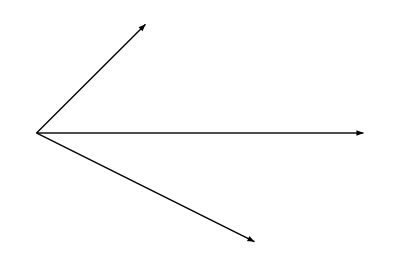

```mathematica
u⃗={1,1};v⃗={2,-1}
Show[Graphics[{
Arrow[{{0,0},u⃗}],
Arrow[{{0,0},v⃗}],
Arrow[{{0,0},u⃗+v⃗}]
}],GridLines->Automatic]
```

```mathematica
A v⃗=λ v⃗
A v⃗=(λI)v⃗
(A-λI)v⃗=OverVector[0]
⇒det(A-λI)=0
```